```mathematica
(* Задача 1 ---------------------------------------------------------------------------*)
```

```mathematica
xs = {6,9,12,14};
ys = {74,77,86.61,102.60};
```

```mathematica
(* От дадените ни данни, можем да заключим,че  функцията ще расте, тоест последният базис {1,e^-x,e^(-2x),e^(-3x),e^(-4x)}отпада защото при него функцията ще намалява, заедно със тригонометричният базис понеже данните за него трябва да са от -1 до 1 и ще се наложи да правим смяна на променливата, което не мисля че е нужно в нашият случай. ще направим за другите варианти, за да видим кой от всичките е най-подходящ *)
```

```mathematica
P[x_] = a0+a1*x +a2*x^2+a3*x^3;
P1[x_] = a0+a1*E^x +a2*E^(2x)+a3*E^(3x);
```

```mathematica
sol = NSolve[{P[xs[[1]]] ==ys[[1]],P[xs[[1]]] ==ys[[1]],P[xs[[2]]] ==ys[[2]],P[xs[[3]]] ==ys[[3]],P[xs[[4]]] ==ys[[4]] }, {a0,a1,a2,a3,a4}];
P[x_] = P[x]/.sol[[1]]
```

39.95+12.7817 x-1.62778 x^2+0.0738889 x^3

```mathematica
sol1= NSolve[{P1[xs[[1]]] ==ys[[1]],P1[xs[[1]]] ==ys[[1]],P1[xs[[2]]] ==ys[[2]],P1[xs[[3]]] ==ys[[3]],P1[xs[[4]]] ==ys[[4]] }, {a0,a1,a2,a3,a4}];
P1[x_] = P1[x]/.sol1[[1]]
```

73.8353+0.00040907 ⅇ^x-2.29894×10^-9 ⅇ^(2 x)+1.64532×10^-15 ⅇ^(3 x)

```mathematica
(* ШЕ построим графиките им *)
```

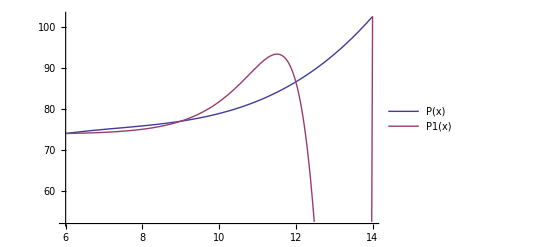

```mathematica
Plot[{P[x],P1[x]},{x,xs[[1]],xs[[4]]}, PlotLegends->"Expressions"]
```

```mathematica
(* От тук виждаме, че при базисът {1,e^x,e^(2x),e^(3x),e^(4x)} се получават отрицателни стойности между 12 и 14, което според дадените ни данни не е възможно. Можехме да заключим още от началото, че това не е нашият нужен базис защото нашата функция не расте бързо.  *)
```

```mathematica
(* Най-подходящ е алгебричният базис {1,х,х^2,х^3} Ще покажем полинома му*)
P[x]
```

39.95+12.7817 x-1.62778 x^2+0.0738889 x^3

```mathematica
(* Задача 2 -------------------------------------------------------------------------------- *)
```

```mathematica
f[x_] = √(5x);
```

```mathematica
(* От условието знаем, че полиномът ни трябва да бъде от степен 3*)
```

```mathematica
n = 3;
xses = Range[2,3.5,0.5];
```

```mathematica
(*Търсим оценка на грешката. Ще я направим чрез теоремата за оценка на грешката*)
```

```mathematica
R[x_,K_]  = (D[f[K],{K,n+1}] (x-xses[[1]])(x-xses[[2]])(x-xses[[3]])(x-xses[[4]]))/((n+1)!) //Abs
```

5/128 √5 Abs[((-3.5+x) (-3.+x) (-2.5+x) (-2.+x))/K^(7/2)]

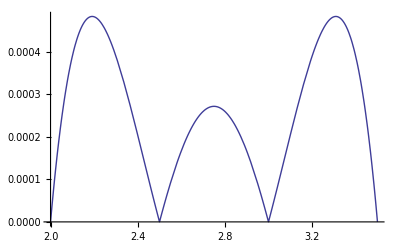

```mathematica
(* Искаме да изберем К да е такова че стойността на 4-тата производна във функцията да е най-голяма. Ще използваме  K = 2 , защото е в знаменател и тогава трябва да вземем най-малкото възможно К от интервала [2,3.5]. *)

Plot[{R[x,xses[[1]]]},{x,xses[[1]],xses[[4]]}]
```

```mathematica
(* Задача 3 -------------------------------------------------------------------------------- *)
```

```mathematica
Lagrange[n_,x0_,h_,f_]:= (
temp = f;
F[x_] = temp;
xS = {x0};

(* Формиране на възлите и стойностите на функцията в тях*)
For[i=1,i<n+1,i++,
	AppendTo[xS,x0+i*h];
];
ys = F[xS];

Basises = {};
currentIndex = 1;
index = 1;
tempBasis = 1;
(* Пресмятане на базиси *)
While[index ≠ n+2,
For[i=1, i<=n+1,i++,
If[currentIndex ≠ i,
	tempBasis *= (x-xS[[i]])/(xS[[currentIndex]] - xS[[i]])
]
]
AppendTo[Basises,tempBasis];
tempBasis =1;
index ++;
currentIndex++;
];

(* Пресмятане на полинома *)

Poly =0;
For[i=1, i<=n+1,i++,
Poly += ys[[i]]*Basises[[i]];
];

Poly//Expand
)
```

```mathematica
Lagrange[2,0,Pi/4,Cos[x]]
```

1-(6 x)/π+(4 √2 x)/π+(8 x^2)/π^2-(8 √2 x^2)/π^2